```mathematica
ClearAll["Global`*"]
```

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../../../Tools/Mathematica/triangulation.nb"]
```

```mathematica
Ω=Circle[]
```

Circle[{0,0}]

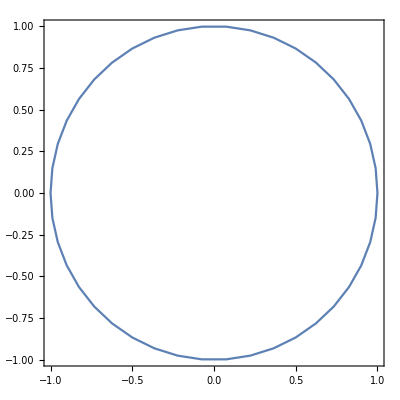

```mathematica
RegionPlot@Ω
```

```mathematica
𝒯=create𝒯fromRegion[Ω,.05];
```

```mathematica
𝒯
```

<|format→NTN,nodes→{{-0.474807,-0.88009},{-0.591849,-0.806049},{-0.697538,-0.716547},{-0.787328,-0.616534},{-0.858722,-0.512441},{-0.916435,-0.400184},{-0.961822,-0.273674},{-0.99041,-0.138162},{-1.,-4.65644×10^-15},{-0.990147,0.14003},{-0.960783,0.2773},{-0.91339,0.407085},{-0.850894,0.525337},{-0.77876,0.627321},{-0.707107,0.707107},{-0.627321,0.778761},{-0.525337,0.850894},{-0.407085,0.91339},{-0.2773,0.960783},{-0.14003,0.990147},{1.31063×10^-22,1.},{0.14003,0.990147},{0.2773,0.960783},{0.407085,0.91339},{0.525337,0.850894},{0.627321,0.77876},{0.707107,0.707107},{0.77876,0.627321},{0.850894,0.525337},{0.91339,0.407085},{0.960783,0.2773},{0.990147,0.14003},{1.,-4.66294×10^-15},{0.990147,-0.14003},{0.960783,-0.2773},{0.91339,-0.407085},{0.850894,-0.525337},{0.778761,-0.627321},{0.707107,-0.707107},{0.627321,-0.77876},{0.525338,-0.850894},{0.407085,-0.91339},{0.2773,-0.960783},{0.14003,-0.990147},{0.,-1.},{-0.123371,-0.992361},{-0.244857,-0.969559},{-0.362603,-0.931944},{-0.143694,-0.765598},{-0.339645,-0.734942},{-0.0539869,-0.871851},{0.448457,-0.634038},{-0.448457,0.634038},{-0.269301,-0.842978},{0.583631,-0.649866},{-0.583631,0.649866},{0.634038,0.448457},{0.66147,-0.46786},{-0.66147,0.46786},{0.649866,0.583631},{0.46786,0.66147},{-0.512389,-0.605063},{0.158603,-0.741435},{0.407306,-0.770683},{-0.0525487,0.74684},{-0.274231,0.750975},{0.74684,0.0525487},{0.750975,0.274231},{0.530388,-0.519447},{0.747766,-0.273059},{-0.530388,0.519447},{-0.747766,0.273059},{0.519447,0.530388},{0.273059,0.747766},{-0.714862,-0.25647},{-0.650959,-0.584417},{0.0056175,-0.730533},{0.29401,-0.662045},{0.0601923,0.855472},{-0.409882,0.775558},{0.855472,-0.0601923},{0.775558,0.409882},{0.514259,-0.286131},{-0.286284,0.431501},{-0.856107,0.183133},{-0.514258,0.28613},{0.431501,0.286285},{0.28613,0.514258},{-0.768168,-0.394923},{-0.791507,-0.0549416},{-0.551901,-0.394915},{0.338772,-0.469029},{-0.855818,-0.180541},{-0.694855,0.0990862},{0.110417,0.690529},{0.690529,-0.110417},{-0.1312,-0.483378},{0.119706,-0.519924},{-0.0471363,0.498534},{0.498533,0.0471363},{-0.570557,-0.0862489},{-0.347025,-0.465183},{-0.0478798,0.0410734},{-0.380739,-0.229673},{0.161282,-0.201974},{0.224714,0.099354},{-0.324856,0.0416075}},triangles→{{75,2,61},{80,95,69},{80,34,33},{61,1,49},{3,2,75},{7,92,89},{90,103,100},{88,3,75},{1,0,49},{85,58,71},{50,53,45},{57,35,69},{86,56,72},{44,50,45},{53,49,47},{82,57,69},{31,67,66},{4,88,5},{47,49,0},{86,67,56},{77,51,91},{59,28,27},{7,6,92},{5,88,6},{66,80,31},{57,68,54},{70,55,58},{11,10,71},{44,43,50},{1,61,2},{76,48,50},{55,70,52},{55,52,79},{13,58,55},{57,54,37},{57,36,35},{15,14,55},{15,55,16},{53,46,45},{79,65,17},{12,11,58},{100,103,106},{16,79,17},{62,43,42},{53,50,48},{83,70,85},{42,41,63},{83,65,52},{60,23,73},{63,40,54},{39,38,54},{42,63,62},{77,63,51},{54,40,39},{83,52,70},{54,51,63},{34,69,35},{62,63,77},{71,58,11},{46,53,47},{67,30,29},{19,78,20},{78,21,20},{30,67,31},{49,48,96},{62,50,43},{50,62,76},{28,81,29},{59,60,72},{56,59,72},{82,91,68},{58,13,12},{78,19,64},{18,65,19},{57,37,36},{38,37,54},{14,13,55},{18,17,65},{23,22,73},{56,81,59},{26,25,59},{10,84,71},{60,59,25},{60,24,23},{31,80,32},{80,33,32},{84,10,9},{27,26,59},{81,67,29},{68,51,54},{60,25,24},{41,40,63},{19,65,64},{48,49,53},{87,60,73},{98,65,83},{78,22,21},{98,102,105},{96,48,76},{89,93,84},{90,75,61},{92,88,74},{77,91,97},{101,90,61},{68,91,51},{68,57,82},{94,78,64},{22,78,73},{55,79,16},{52,65,79},{95,80,66},{34,80,69},{59,81,28},{56,67,81},{67,86,99},{72,87,86},{58,85,70},{95,66,99},{9,8,84},{89,8,7},{93,71,84},{88,90,74},{72,60,87},{102,98,83},{78,94,73},{94,64,98},{3,88,4},{90,88,75},{100,74,90},{84,8,89},{96,101,49},{100,93,89},{97,91,104},{97,62,77},{88,92,6},{74,89,92},{100,89,74},{85,71,93},{64,65,98},{87,73,94},{66,67,99},{82,69,95},{97,76,62},{104,102,96},{99,105,104},{76,97,96},{83,85,106},{87,94,98},{87,98,105},{82,95,99},{90,101,103},{93,100,106},{49,101,61},{96,102,103},{104,96,97},{86,105,99},{96,103,101},{106,103,102},{91,82,104},{99,104,82},{87,105,86},{104,105,102},{83,106,102},{93,106,85}},neighbors→{{29,100,4},{141,111,110},{-1,85,111},{8,152,29},{0,7,-1},{135,119,22},{41,128,150},{4,127,126},{18,3,-1},{58,137,116},{38,13,44},{56,15,35},{69,115,19},{10,-1,28},{18,59,93},{11,141,105},{140,24,63},{23,-1,126},{8,-1,14},{113,12,114},{104,102,52},{-1,87,112},{134,5,-1},{134,-1,17},{84,16,110},{89,34,105},{33,116,31},{81,58,-1},{65,13,-1},{0,-1,3},{44,66,98},{54,32,26},{109,108,31},{26,76,71},{75,74,25},{-1,11,74},{76,37,-1},{108,-1,36},{-1,10,59},{77,42,109},{58,71,-1},{157,151,6},{39,-1,108},{-1,51,65},{30,93,10},{116,146,54},{91,51,-1},{109,54,95},{78,94,83},{53,55,91},{75,53,-1},{57,43,46},{55,20,57},{-1,50,49},{31,45,47},{52,49,89},{11,-1,111},{52,133,51},{40,27,9},{14,-1,38},{-1,88,63},{62,-1,72},{-1,61,96},{16,-1,60},{98,130,93},{28,43,66},{142,30,65},{88,-1,112},{122,69,82},{68,12,79},{104,105,158},{-1,40,33},{92,106,61},{92,-1,77},{-1,35,34},{34,50,-1},{33,36,-1},{39,73,-1},{107,48,-1},{112,69,113},{82,87,-1},{120,27,86},{80,90,68},{-1,48,90},{85,-1,24},{-1,84,2},{-1,118,81},{80,21,-1},{60,67,113},{55,25,104},{-1,83,82},{49,46,-1},{138,72,73},{14,44,64},{48,139,122},{47,123,138},{-1,62,107},{161,148,123},{30,145,64},{120,129,131},{0,103,127},{121,135,134},{132,133,20},{100,152,150},{20,89,70},{15,70,25},{72,125,124},{124,78,96},{42,37,32},{39,32,47},{24,117,1},{1,56,2},{67,21,79},{88,79,19},{155,140,19},{160,12,122},{45,26,9},{140,149,110},{129,86,-1},{-1,5,129},{81,99,137},{128,101,127},{94,115,68},{95,162,97},{139,107,106},{138,147,106},{17,-1,7},{7,100,121},{121,6,136},{119,99,118},{152,64,156},{99,136,151},{158,154,102},{57,102,142},{22,23,101},{5,101,136},{135,128,131},{120,163,9},{95,125,92},{124,147,94},{114,117,16},{1,149,15},{66,133,145},{153,154,161},{161,159,155},{154,98,142},{163,162,45},{125,148,139},{97,160,147},{117,159,141},{156,6,103},{41,163,131},{103,3,130},{157,156,143},{145,132,143},{144,114,160},{150,130,153},{153,162,41},{159,132,70},{158,149,144},{155,115,148},{97,143,144},{157,123,146},{146,137,151}},ribs→{}|>

```mathematica
Show[highlight[𝒯,{"nodesNumn","localNodesNumn","trianglesNumn"}],ImageSize->Full]
```

-Graphics-